```mathematica
(* Distribution Calculator using the LMA for Nonlinear Feedback Loop shown in Fig 1A upper in the paper *)
(* Authors: Zhixing Cao & Ramon Grima @ University of Edinburgh *)
```

```mathematica
(* Clear cache *)
Clear["Global`*"]
```

{0.208663,Null}

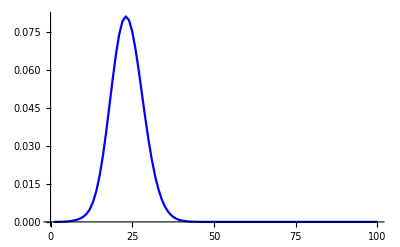

```mathematica
(* Variable Define *)
(* For steady state solution, set TimeDep = 0; For time dependent solution, set TimeDep = 1 *)
TimeDep=1;
Timing[
Σ=1+Subscript[σ, b]+Subscript[σ, u];
Subscript[ρ, Δ]=Subscript[ρ, b]-Subscript[ρ, u];

(* Input Time of Interest *)
T=0.5;

(* Input rate parameter values *)
(* λ is the mean number of proteins in the Poisson distribution at t = 0; set to zero if zero proteins initially *)
param={Subscript[ρ, u]->60,Subscript[ρ, b]->25,Subscript[σ, b]->0.004,Subscript[σ, u]->0.25,λ->0};

(* Moment equations for <np>, <ng> and <npng> respectively of the linear networks generated by the LMA *)
If[TimeDep==1,{
eq1 = Subscript[ρ, u]*ng[t]+Subscript[ρ, b]*(1-ng[t])-np[t];
eq2 = -Subscript[σ̄, b]*ng[t]+Subscript[σ, u]*(1-ng[t])/.Subscript[σ̄, b]->Subscript[σ, b]*npng[t]/ng[t];
eq3 =Subscript[ρ, u]*ng[t]+Subscript[σ, u]*np[t]-(1+Subscript[σ̄, b]+Subscript[σ, u])*npng[t]/.Subscript[σ̄, b]->Subscript[σ, b]*npng[t]/ng[t];

(* Compute the effective rate parameter Subscript[σ̄, b] *)
sol=Flatten[NDSolve[{np'[t]==eq1/.param,ng'[t]==eq2/.param,npng'[t]==eq3/.param,np[0]==λ/.param,ng[0]==1,npng[0]==λ/.param},{np,ng,npng},{t,0,T}]];
solInt=Table[Subscript[σ, b]*npng[t]/ng[t]/.sol/.param/.t->i,{i,0.001,T,0.001}];
Subscript[σ̄, b]= Sum[solInt[[i]]*0.001,{i,1,T/0.001}]/T},
Subscript[σ̄, b]=1/2*(-1+Subscript[ρ, b]*Subscript[σ, b]-Subscript[σ, u]+Sqrt[(-1+Subscript[ρ, b]*Subscript[σ, b]-Subscript[σ, u])^2+4*Subscript[ρ, u]*Subscript[σ, b]*(1+Subscript[σ, u])])/.param];
(* If Subscript[ρ, u] ≤ Subscript[ρ, b] then for numerically stable solution switch the position of Subscript[ρ, u] and Subscript[ρ, b] as well as Subscript[σ̄, b] and Subscript[σ, u], since the linear network topology is symmetric *)
paramt={rut->Subscript[ρ, u]/.param,rbt->Subscript[ρ, b]/.param,sut->Subscript[σ, u]/.param,Lambdat->λ/.param};
If[(Subscript[ρ, u]/.param)<=(Subscript[ρ, b]/.param),paramN={Subscript[ρ, u]->rbt/.paramt,Subscript[ρ, b]->rut/.paramt,Subscript[σ, b]->sut/.paramt,Subscript[σ, u]->Subscript[σ̄, b],λ->Lambdat/.paramt},paramN={Subscript[ρ, u]->rut/.paramt,Subscript[ρ, b]->rbt/.paramt,Subscript[σ, b]->Subscript[σ̄, b],Subscript[σ, u]->sut/.paramt,λ->Lambdat/.paramt}];

(* Full Generating Function Solution *)
t=T;
If[TimeDep==1,
f=Subscript[σ, b]/(Σ-1)*(-Subscript[ρ, Δ]*w*Exp[-t])^(Σ-1)*Exp[λ*w-Subscript[ρ, u]*w*Exp[-t]+Subscript[ρ, b]*w]*Hypergeometric1F1[Subscript[σ, u],Σ,-Subscript[ρ, Δ]*w*Exp[-t]],
f=0];

F = f*(-Subscript[ρ, Δ]*w)^(1-Σ)*Hypergeometric1F1[1-Subscript[σ, b],2-Σ,-Subscript[ρ, Δ]*w];

If[TimeDep==1,
g=Subscript[σ, u]/(Σ-1)*Exp[λ*w-Subscript[ρ, u]*w*Exp[-t]+Subscript[ρ, b]*w]*Hypergeometric1F1[-Subscript[σ, b],2-Σ,-Subscript[ρ, Δ]*w*Exp[-t]],
g=Subscript[σ, u]/(Subscript[σ, u]+Subscript[σ, b])*Exp[Subscript[ρ, b]*w]];

G=g*Hypergeometric1F1[1+Subscript[σ, u],Σ,-Subscript[ρ, Δ]*w];
sP0=(F+G);
sP1=1/Subscript[σ, u]*(-Subscript[σ, u]*(-Subscript[ρ, Δ]*w)^(1-Σ)*Hypergeometric1F1[-Subscript[σ, b],2-Σ,-Subscript[ρ, Δ]*w]*f+Subscript[σ, b]*Hypergeometric1F1[Subscript[σ, u],Σ,-Subscript[ρ, Δ]*w]*g);
Gsol =(sP0+sP1)/.paramN;

(* Distribution  Computation *)
(* Span of protein numbers *)
Bins=100;
v=Table[0,{i,1,Bins}];
v[[1]]=Series[Gsol,{w,-1,Bins}];
For[i=2,i≤Bins,i++,v[[i]]=SeriesCoefficient[v[[1]],{w,-1,i}]];
v[[1]]=SeriesCoefficient[v[[1]],{w,-1,1}];]
P=ListPlot[v,PlotStyle->{Blue},PlotRange->All,Joined->True];
Show[{P}]
(* Output CPU Time and distribution *)
```

```mathematica
(* Note that the combination of large absolute value of |λ-Subscript[ρ, u] Exp[-t]+Subscript[ρ, b]| and small value of T may cause numerical instability issues. *)
```